```mathematica
SetDirectory[NotebookDirectory[]]
```

H:\Sandro\Data\Documents\02_FPP\03_classes\1.stopnja\IPFM_01\lectures\grm\01_geometrija_in_vektorji\figs

## Primer - optični kabel

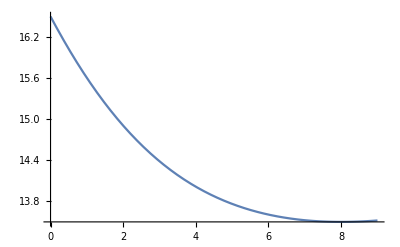

fig_01_12.pdf

```mathematica
pl=Plot[9-x+1.25 Sqrt[36+x^2],{x,0,9}]
Export["fig_01_12.pdf",pl]
```

```mathematica
ss=Series[9-x+1.25 Sqrt[36+x^2],{x,8,4}]//Normal
```

13.5+0.0225 (-8+x)^2-0.0018 (-8+x)^3+0.00012375 (-8+x)^4

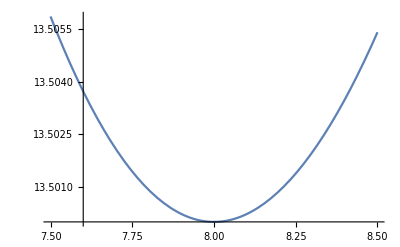

```mathematica
Plot[ss,{x,7.5,8.5}]
```

```mathematica
tf=9-x+1.25 Sqrt[36+x^2]/.x->8-ϵ//Simplify
```

1+1.25 √(36+(-8+ϵ)^2)+ϵ

```mathematica
Series[tf,{ϵ,0,2}]
```

13.5+0.0225 ϵ^2+O[ϵ]^3